```mathematica
/Users/warren/Documents/Princeton/EGR191/Lab 7/Mathematica Code
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[(M2/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+33.7402 t-1. gt t}}

-0.199024+33.7402 t-1. gt t

-0.199024 t+16.8701 t^2-0.5 gt t^2

33.7402-1. gt

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]}}

-0.199024-1. gt t-26.0768 t Log[1.45159 (0.6889-1. M0t)]

-0.199024 t-0.5 gt t^2-13.0384 t^2 Log[1.45159 (0.6889-1. M0t)]

-1. gt-26.0768 Log[1.45159 (0.6889-1. M0t)]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u Log[((M1-M0*t)/M1)]-gt,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

{{v[t]→-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-1. gt t+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-0.5 gt t^2-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-1. gt-26.0768/(1.-2.68309 t)+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

-Graphics-

{{v[t]→-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]}}

-0.199024+26.0768 t-4.905 t^2+9.71894 Log[1.-2.68309 t]-26.0768 t Log[1.-2.68309 t]

-5.0585 t+19.5576 t^2-1.635 t^3-1.81115 Log[1.-2.68309 t]+9.71894 t Log[1.-2.68309 t]-13.0384 t^2 Log[1.-2.68309 t]

26.0768-26.0768/(1.-2.68309 t)-9.81 t+(69.9664 t)/(1.-2.68309 t)-26.0768 Log[1.-2.68309 t]

26.0768

0.1889

0.6889

1.84838

9.81

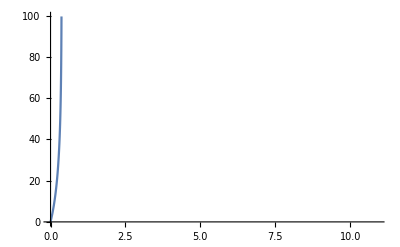

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==w1},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```

```mathematica
ClearAll
```

ClearAll

```mathematica
sol2=DSolve[{v'[t]==-u*Log[((M1-M0*t)/M1)]-g*t,v[0]==0},v[t],t]
vsol2[t_]=v[t]/.sol2[[1]]
h2[t_]=Integrate[vsol2[t],t]
a2[t_]=D[vsol2[t],t]

u=26.07680962
M2=.1889
M1=.6889
M0=1.8483812
g=9.81

Plot[a2[t],{t,0,10.91}]
```